```mathematica
gpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-t-up-xi1-pi-noD.wdx"];
Hdgu=Query[1,1]@gpdu;
Heru=Query[1,2]@gpdu;
Hdau=Query[1,3]@gpdu;
Edgu=Query[2,1]@gpdu;
Eeru=Query[2,2]@gpdu;
Edau=Query[2,3]@gpdu;
Hdgfu=Interpolation[Flatten[Hdgu,1]];
Herfu=Interpolation[Flatten[Heru,1]];
Hdafu=Interpolation[Flatten[Hdau,1]];
Edgfu=Interpolation[Flatten[Edgu,1]];
Eerfu=Interpolation[Flatten[Eeru,1]];
Edafu=Interpolation[Flatten[Edau,1]];
```

```mathematica
Dgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-t-D-xi1-pi.wdx"];

dHeru=Query[1,2]@Dgpdu;
dHdau=Query[1,3]@Dgpdu;

dEeru=Query[2,2]@Dgpdu;
dEdau=Query[2,3]@Dgpdu;

dHerfu=Interpolation[Flatten[dHeru,1]];
dHdafu=Interpolation[Flatten[dHdau,1]];

dEerfu=Interpolation[Flatten[dEeru,1]];
dEdafu=Interpolation[Flatten[dEdau,1]];
```

```mathematica
Herall[x_,t_]:=Herfu[x,-t]+Hdafu[x,-t]+dHerfu[x,-t]+dHdafu[x,-t];
Eerall[x_,t_]:=Eerfu[x,-t]+Edafu[x,-t]+dEerfu[x,-t]+dEdafu[x,-t];
```

```mathematica
Herall2[x_,t_]:=Herfu[x,-t]+Hdafu[x,-t];
Eerall2[x_,t_]:=Eerfu[x,-t]+Edafu[x,-t];
```

```mathematica
pHd2=Show[Plot3D[I*Hdgfu[x,-t],{x,0.1,1},{t,0.037,1},PlotRange->All],Plot3D[I*Herall2[x,t],{x,-0.1,0.1},{t,0.037,1},PlotRange->All],
Graphics3D[Text[Style["x",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.42,-0.22,0.1}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],280Degree],Scaled[{-0.18,-0.1,0.65}]]],Graphics3D[Text[Style["H_d",Black,30,FontFamily->Times],Scaled[{1.16,0,0.6}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,-1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{-0.7,-2,0.8}]
pEd2=Show[Plot3D[I*Edgfu[x,-t],{x,0.1,1},{t,0.037,1},PlotRange->All],Plot3D[Re[I*Eerall2[x,t]],{x,-0.1,0.1},{t,0.037,1},PlotRange->All],
Graphics3D[Text[Style["x",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.42,-0.22,0.1}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],280Degree],Scaled[{-0.18,-0.1,0.65}]]],Graphics3D[Text[Style["E_d",Black,30,FontFamily->Times],Scaled[{1.18,0,0.6}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,-1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{-0.7,-2,0.8}]
```

-Graphics3D-

-Graphics3D-

```mathematica
pHd=Show[Plot3D[I*Hdgfu[x,-t],{x,0.1,1},{t,0.037,1},PlotRange->All],Plot3D[I*Herall[x,t],{x,-0.1,0.1},{t,0.037,1},PlotRange->All],
Graphics3D[Text[Style["x",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.42,-0.22,0.1}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],280Degree],Scaled[{-0.18,-0.1,0.65}]]],Graphics3D[Text[Style["H_d",Black,30,FontFamily->Times],Scaled[{1.16,0,0.6}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,-1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{-0.7,-2,0.8}]
pEd=Show[Plot3D[I*Edgfu[x,-t],{x,0.1,1},{t,0.037,1},PlotRange->All],Plot3D[Re[I*Eerall[x,t]],{x,-0.1,0.1},{t,0.037,1},PlotRange->All],
Graphics3D[Text[Style["x",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.42,-0.22,0.1}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],280Degree],Scaled[{-0.18,-0.1,0.65}]]],Graphics3D[Text[Style["E_d",Black,30,FontFamily->Times],Scaled[{1.18,0,0.6}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,-1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{-0.7,-2,0.8}]
```

-Graphics3D-

-Graphics3D-

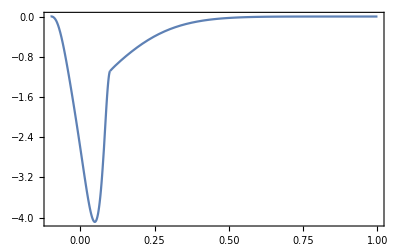
-Graphics-H_dx

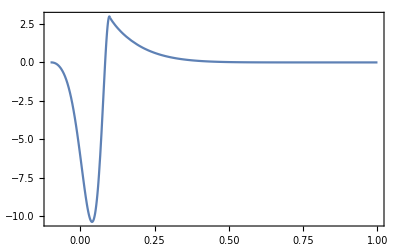
-Graphics-E_dx

```mathematica
pHd2d2=Labeled[Show[Plot[I*Hdgfu[x,-1],{x,0.1,1},PlotRange->All],Plot[I*Herall2[x,1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"H_d",
"x"},{Left,Bottom},LabelStyle->24]
pEd2d2=Labeled[Show[Plot[I*Edgfu[x,-1],{x,0.1,1},PlotRange->All],Plot[Re[I*Eerall2[x,1]],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"E_d",
"x"},{Left,Bottom},LabelStyle->24]
```

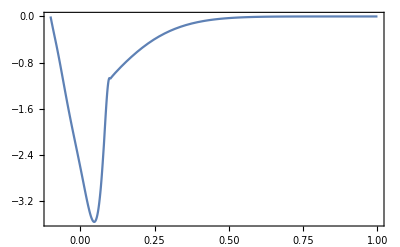
-Graphics-H_dx

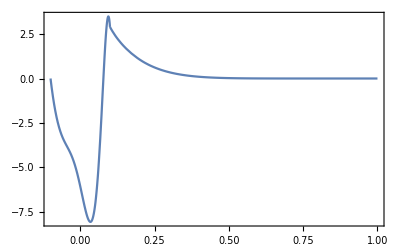
-Graphics-E_dx

```mathematica
pHd2d=Labeled[Show[Plot[I*Hdgfu[x,-1],{x,0.1,1},PlotRange->All],Plot[I*Herall[x,1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"H_d",
"x"},{Left,Bottom},LabelStyle->24]
pEd2d=Labeled[Show[Plot[Re[I*Edgfu[x,-1]],{x,0.1,1},PlotRange->All],Plot[I*Eerall[x,1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"E_d",
"x"},{Left,Bottom},LabelStyle->24]
```

```mathematica
pathH2=FileNameJoin[{"C:\\Users\\DELL\\Desktop\\73diagram",
"H3d-f-noD.pdf"}];
Export[pathH2,pHd2]


pathE2=FileNameJoin[{"C:\\Users\\DELL\\Desktop\\73diagram",
"E3d-f-noD.pdf"}];
Export[pathE2,pEd2]


pathH2d2=FileNameJoin[{"C:\\Users\\DELL\\Desktop\\73diagram",
"H2d-f-noD.pdf"}];
Export[pathH2d2,pHd2d2]
pathE2d2=FileNameJoin[{"C:\\Users\\DELL\\Desktop\\73diagram",
"E2d-f-noD.pdf"}];
Export[pathE2d2,pEd2d2]
```

C:\Users\DELL\Desktop\73diagram\H3d-f-noD.pdf

C:\Users\DELL\Desktop\73diagram\E3d-f-noD.pdf

C:\Users\DELL\Desktop\73diagram\H2d-f-noD.pdf

C:\Users\DELL\Desktop\73diagram\E2d-f-noD.pdf

```mathematica
pathH=FileNameJoin[{"C:\\Users\\DELL\\Desktop\\73diagram",
"H3d-f-D.pdf"}];
Export[pathH,pHd]


pathE=FileNameJoin[{"C:\\Users\\DELL\\Desktop\\73diagram",
"E3d-f-D.pdf"}];
Export[pathE,pEd]


pathH2d=FileNameJoin[{"C:\\Users\\DELL\\Desktop\\73diagram",
"H2d-f-D.pdf"}];
Export[pathH2d,pHd2d]
pathE2d=FileNameJoin[{"C:\\Users\\DELL\\Desktop\\73diagram",
"E2d-f-D.pdf"}];
Export[pathE2d,pEd2d]
```

C:\Users\DELL\Desktop\73diagram\H3d-f-D.pdf

C:\Users\DELL\Desktop\73diagram\E3d-f-D.pdf

C:\Users\DELL\Desktop\73diagram\H2d-f-D.pdf

C:\Users\DELL\Desktop\73diagram\E2d-f-D.pdf